```mathematica
ClearAll["Global`*"];
```

```mathematica
t1=1.2;t2=-1;μ=0.2;γ=0.1;λ=-1;
hsk[k_]:=(t1+t2 Cos[k]){{0,1},{1,0}}+t2 Sin[k]{{0,-I},{I,0}}-μ {{1,0},{0,-1}}+λ Sin[k]{{1,0},{0,-1}}-I({{γ, 0}, {0, γ}});
```

```mathematica
ty=3.5;tx=1;μ2=0.3;
Ny=300;n=2Ny;
HPBC[k_]:=SparseArray[Band[{1,2},{n-1,n},2]->tx(1+Exp[-I k]),{n,n}]+SparseArray[Band[{2,1},{n,n-1},2]->tx (1+Exp[I k]),{n,n}]+SparseArray[Band[{1,3},{n-2,n}]->ty,{n,n}]+SparseArray[Band[{3,1},{n,n-2}]->ty,{n,n}]-SparseArray[Band[{1,1},{n,n}]->{μ2,μ2},{n,n}]-I SparseArray[Band[{1,1},{n,n}]->{γ,γ},{n,n}];
```

```mathematica
TA=0.6;TB=0;nk=80;
Hcoup=SparseArray[Band[{1,1},{2,2}]->{TA,TB},{2,n}];
Htot[k_]:=Join[Join[hsk[k],Hcoup,2],Join[Conjugate[Transpose[Hcoup]],HPBC[k],2]];Gext[k_,w_]:=(Inverse[w IdentityMatrix[n+2]-N[Htot[k]]])[[1;;2,1;;2]];Aext[w_]:=-1/(nk Pi)Sum[Im[Tr[Gext[2Pi/nk i,w]]],{i,1,nk}];
```

```mathematica
E1[k_,w_]:=w+I γ-(-μ2-2 tx Cos[k/2]);E2[k_,w_]:=w+I γ-(-μ2+2 tx Cos[k/2]);
f1[k_,w_]:=FromContinuedFraction[Table[If[OddQ[i],E1[k,w],-E1[k,w]/ty^2],{i,1,Ny}]];f2[k_,w_]:=FromContinuedFraction[Table[If[OddQ[i],E2[k,w],-E2[k,w]/ty^2],{i,1,Ny}]];MInv11[k_,w_]:=TA^2/2*(1/f1[k,w]+1/f2[k,w]);G[k_,w_]:=Inverse[w IdentityMatrix[2]-hsk[k]-{{MInv11[k,w],0},{0,0}}];
A[w_]:=-1/(nk Pi)Sum[Im[Tr[G[2Pi/nk i,w]]],{i,1,nk}];
```

```mathematica
evs=ParallelTable[Eigenvalues[N[Htot[k]]],{k,-Pi,Pi,2Pi/80}];
```

```mathematica
filteredEigenvalues=Select[Flatten[evs],-3<=Re[#]<=3&];
```

```mathematica
filteredSparse=filteredEigenvalues[[;;;;20]];
```

```mathematica
DOS1=Transpose[ParallelTable[A[wr+I wi],{wr,-3,3,0.005},{wi,-0.25-10^-10 ,-0.05-10^-10,0.002}]];
```

```mathematica
Col1[x_]:=If[x>0,RGBColor[1,0,0,(x/5)^1],RGBColor[0,0,1,(-x/5)^1]];
```

```mathematica
A3b=ListDensityPlot[DOS1,ColorFunction->Col1,ColorFunctionScaling->False,PlotRange->{-10,10},DataRange->{{-3,3},{-0.25,-0.05}},LabelStyle->{FontFamily->"Times New Roman",25,GrayLevel[0]},BaseStyle->{FontFamily->"Times New Roman",25},FrameLabel->{{"Im ω",None},{"Re ω",None}},AspectRatio->1,ImageSize->390,PlotTheme->"Scientific"]
```

-Graphics-

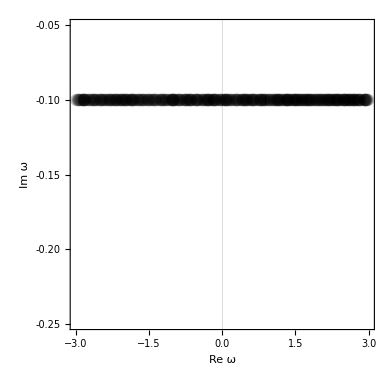

```mathematica
A3a=ListPlot[ReIm[filteredSparse],PlotTheme->"Scientific",PlotMarkers->{Graphics/@{Circle[{0,0},1]},0.02},PlotStyle->{Black,Thickness[0.15],Opacity[0.1]},PlotRange->{{-3,3},{-0.25,-0.05}},LabelStyle->{FontFamily->"Times New Roman",25,GrayLevel[0]},BaseStyle->{FontFamily->"Times New Roman",25},FrameLabel->{{"Im ω",None},{"Re ω",None}},FrameTicks->{{{-0.25,{-0.2,"-0.20"},-0.15,{-0.10,"-0.10"},-0.05},Automatic},{Automatic,Automatic}},AspectRatio->1,ImageSize->390]
```

```mathematica
Show[{A3a,A3b}]
```

-Graphics-